Effect of the mode (k,l)   (k=1,2,...  l=0,1,...)

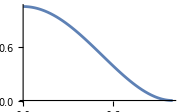

```mathematica
k=1; l=0;
rs=1*^-0;
(*rs_large =1*^-2;*)
(*rs_small =2*^-5;*)
f[x_, l_]=BesselJ[l,x]BesselI[l+1,x]+BesselI[l,x]BesselJ[l+1,x];
rootsNumeric=NSolve[{f[x,l]==0, 0<x<=100}, x, Reals] // N[#,10]&;
roots = x /. rootsNumeric;
u[r_,θ_]=(BesselJ[l,roots[[k]]r/rs]-(BesselJ[l,roots[[k]]]/BesselI[l,roots[[k]]])BesselI[l,roots[[k]]r/rs])Cos[l θ];
Plot[u[r*rs,0], {r,0,1}]
```

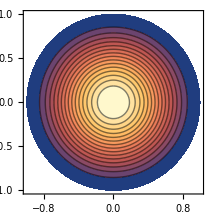

```mathematica
tf = TransformedField["Polar"->"Cartesian",u[r*rs,θ], {r,θ}->{x,y}];
ContourPlot[tf,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},x^2+y^2<1],Contours->15]
```

Defining the amplitude A = Sqrt[<z.b2>] with respect to the frequency ω = root[k]^2 * d/rs^2 Sqrt[E / (12 rho (1 - nu^2))] = root[k]^2 * 3716 d/rs^2  with E = 110GPa, nu = 1/3 and rho = 8960

```mathematica
hbar=Quantity["ReducedPlanckConstant"];
kB = Quantity["BoltzmannConstant"];
T=Quantity[4,"Kelvins"];
m=Quantity[0.5*8960*Pi*rs^2*(100*^-9), "Kilograms"];
ω=Quantity[roots[[k]]^2/rs^2*1.073*^-4,"Seconds^(-1)"]
DeltaZ=UnitConvert[Sqrt[hbar/(2m ω)Coth[(hbar ω)/(2 kB T)]],"Meters"]
Amplitude=QuantityMagnitude[DeltaZ];
```

0.00109616 per second

1.80711×10^-7 m

## Large Shields

Calculating the angular variance δθ and the length variance δL. These are directly related with the variance of the amplitude δz.

Positioned in the worst-case spot

```mathematica
rMaxGradient =0.5274771443088469*rs;
maxGradient = Abs[D[u[r,0],r]]/.r->rMaxGradient;
(*maximized=Maximize[Abs[D[u[r,0],r]],{r}∈Interval[{0,rs}]];
maxGradient = First[maximized]//N;
rMaxGradient = r/.Last[maximized]//N;*)
Deltaθ = ArcTan[Amplitude*maxGradient]//N;
(* Deltaθ2 = ArcTan[Amplitude*Abs[u[rMaxGradient-50*^-9,0]-u[rMaxGradient+50*^-9,0]]/100*^-9]//N; *)
DeltaL = Amplitude*Abs[u[rMaxGradient,0]]//N;
Quantity[Deltaθ, "Radians"]
Quantity[DeltaL, "Meters"]
```

2.95242×10^-7 rad

9.19858×10^-8 m

Positioned in the center

```mathematica
gradientMiddle = D[u[r,0],r]/.r->0;
Deltaθ = ArcTan[Amplitude*gradientMiddle]//N
DeltaL = Amplitude*u[0,0]//N
```

0.

1.90779×10^-8

## Small Shields

Different to above, the particle is always placed in the center. The effect of the Casimir interactions is upper bounded by the maxima and minima of u_{kl}(x).

```mathematica
maximum = Maximize[u[r,0],{r}∈Interval[{0.1*rs,0.9*rs}]];
minimum = Minimize[u[r,0],{r}∈Interval[{-0.9*rs,-0.1*rs}]];
DeltaR = Abs[(r/.Last[maximum]) - (r/.Last[minimum])];
DeltaAmpl = Amplitude*Abs[First[maximum]-First[minimum]];
Deltaθ = ArcTan[DeltaAmpl / DeltaR]
```

1.27675×10^-7

## Effect of the modes

Effect of the first n modes on  dephasing. Dephasing goes with (k+l)^-8

```mathematica
n = 2;
1/Zeta[8] * Sum[1/k^8, {k, 1, n}]//N
```

0.99983

Effect of the first n modes on the amplitude (goes with (k+l)^-2)

```mathematica
n=5;
1/Zeta[2] * Sum[1/k^2, {k, 1, n}]//N
```

0.889769